```mathematica
competitive={1.21388*^07,4.64632*^06,3.47496*^06,3.22095*^06,3.22905*^06,3.90802*^06,2.84327*^06};
monopoly={1.25823*^07,4.77103*^06,3.58568*^06,3.31037*^06,3.28174*^06,4.06436*^06,2.89229*^06};
```

```mathematica
names={"Saudi Arabia","Iran","Iraq","Kuwait","UAE","Venezula","Nigeria"};
```

```mathematica
totComp=Plus@@competitive;
totMon=Plus@@monopoly;
```

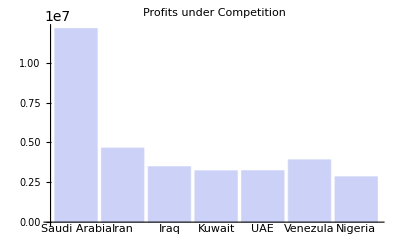

```mathematica
BarChart[competitive,ChartLabels->names,PlotLabel->"Profits under Competition"]
```

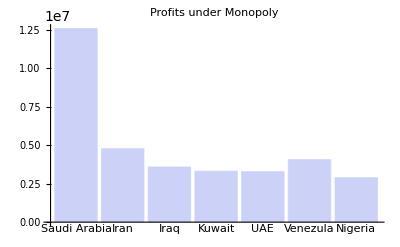

```mathematica
BarChart[monopoly,ChartLabels->names,PlotLabel->"Profits under Monopoly"]
```

```mathematica
pct=(monopoly/competitive)~Join~{totMon/totComp};
pct=pct-1;
pct=pct*100;
```

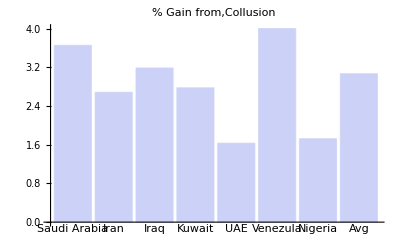

```mathematica
BarChart[pct,ChartLabels->names~Join~{"Avg"},PlotLabel->"% Gain from,Collusion"]
```